#### Libraries

```mathematica
Import[NotebookDirectory[]<>"library_quantumInformation.m"]
Import[NotebookDirectory[]<>"library_graphStates.m"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/alexanderpickston/Dropbox (Heriot-Watt University Team)/RES_EPS_EMQL/userFolders/Alex/sim_notebooks/model_graphStates

### Circuit model

To generate the trident graph need to use some circuit model functions. Where the circuit represents the spatial modes.  Using my library to define the functions needed to create the circuit.

#### Definitions

```mathematica
(* Current definitions of waveplate rotations *)
{HWP[x],QWP[x]}
```

{{{ⅈ Cos[2 x],ⅈ Sin[2 x]},{ⅈ Sin[2 x],-ⅈ Cos[2 x]}},{{(1+ⅈ Cos[2 x])/(√2),(ⅈ Sin[2 x])/(√2)},{(ⅈ Sin[2 x])/(√2),(1-ⅈ Cos[2 x])/(√2)}}}

```mathematica
HWPalt[x_]:={{Cos[2*x],-Sin[2*x]},{Sin[2*x],Cos[2*x]}}
```

```mathematica
QWPalt[x_]:=Exp[-ⅈ*π/4]*{{1,0},{0,ⅈ}}
QWPaltalt[x_]:={{Exp[ⅈ*x],0},{0,Exp[-ⅈ*x]}}
HWPaltalt[x_]:={{Exp[ⅈ*x],0},{0,Exp[-ⅈ*x]}}
```

Testing the different definitions to a case of rotating into the XY plane and then rotating around the XY plane.

```mathematica
operation=(HWPalt[0].QWPalt[π/4])
(1/Sqrt[(#⟦1,1⟧)^2+(#⟦2,1⟧)^2]*#)&@operation//FullSimplify
```

{{ⅇ^(-(ⅈ π)/4),0},{0,ⅈ ⅇ^(-(ⅈ π)/4)}}

{{1,0},{0,ⅈ}}

```mathematica
(HWPalt[π/2].QWPalt[π/4].h)==(QWPalt[π/4].HWPalt[π/2].h)
(HWP[π/2].QWP[π/4].h)==(QWP[π/4].HWP[π/2].h)
(HWPalt[π/2].QWP[π/4].h)==(QWP[π/4].HWPalt[π/2].h)
```

True

False

True

```mathematica
Abs
```

Abs

```mathematica
HWP[π/8]//FullSimplify;
```

```mathematica
circuitHWP[angle_,mode_,time_]:={
w[time,mode,H]->HWP[angle]⟦1,1⟧w[time,mode,H]+HWP[angle]⟦2,1⟧w[time,mode,V],
w[time,mode,V]->HWP[angle]⟦1,2⟧w[time,mode,H]+HWP[angle]⟦2,2⟧w[time,mode,V]
};
```

```mathematica
circuitQWP[angle_,mode_,time_]:={
w[time,mode,H]->QWP[angle]⟦1,1⟧w[time,mode,H]+QWP[angle]⟦2,1⟧w[time,mode,V],
w[time,mode,V]->QWP[angle]⟦1,2⟧w[time,mode,H]+QWP[angle]⟦2,2⟧w[time,mode,V]
};
```

```mathematica
circuitHWPalt[angle_,mode_,time_]:={
w[time,mode,H]->HWPaltalt[angle]⟦1,1⟧w[time,mode,H]+HWPaltalt[angle]⟦2,1⟧w[time,mode,V],
w[time,mode,V]->HWPaltalt[angle]⟦1,2⟧w[time,mode,H]+HWPaltalt[angle]⟦2,2⟧w[time,mode,V]
};
```

```mathematica
circuitQWPalt[angle_,mode_,time_]:={
w[time,mode,H]->QWPaltalt[angle]⟦1,1⟧w[time,mode,H]+QWPaltalt[angle]⟦2,1⟧w[time,mode,V],
w[time,mode,V]->QWPaltalt[angle]⟦1,2⟧w[time,mode,H]+QWPaltalt[angle]⟦2,2⟧w[time,mode,V]
};
```

```mathematica
circuitQWPHWPalt[angleQWP_,angleHWP_,mode_,time_]:={
w[time,mode,H]->HWPalt[angleHWP].QWPalt[angleQWP]⟦1,1⟧w[time,mode,H]+HWPalt[angleHWP].QWPalt[angleQWP]⟦2,1⟧w[time,mode,V],
w[time,mode,V]->HWPalt[angleHWP].QWPalt[angleQWP]⟦1,2⟧w[time,mode,H]+HWPalt[angleHWP].QWPalt[angleQWP]⟦2,2⟧w[time,mode,V]
};
```

```mathematica
PBS[α_,m1_,m2_,t_,δ_:π/2]:={
w[t,m1,H]->Cos[α]^2 w[t,m1,H]+Cos[α]Sin[α] w[t,m1,V]+Exp[I δ](Sin[α]^2 w[t,m2,H]-Cos[α]Sin[α]w[t,m2,V]),
w[t,m1,V]->Sin[α]^2 w[t,m1,V]+Cos[α]Sin[α] w[t,m1,H]+Exp[I δ](Cos[α]^2 w[t,m2,V]-Cos[α]Sin[α]w[t,m2,H]),
w[t,m2,H]->Cos[α]^2 w[t,m2,H]+Cos[α]Sin[α] w[t,m2,V]+Exp[I (π-δ)](Sin[α]^2 w[t,m1,H]-Cos[α]Sin[α]w[t,m1,V]),
w[t,m2,V]->Sin[α]^2 w[t,m2,V]+Cos[α]Sin[α] w[t,m2,H]+Exp[I (π-δ)](Cos[α]^2 w[t,m1,V]-Cos[α]Sin[α]w[t,m1,H])
};
```

```mathematica
DumpHO:=Join[Table[w[t_,m_,H]^i->0,{i,2,10}],Table[w[t_,m_,V]^i->0,{i,2,10}],{w[t_,m_,H]w[t_,m_,V]->0}]
```

```mathematica
PostSelection[state_,cond_]:=Total[Cases[state,_*cond]];
```

```mathematica
SuccessProbability[state_]:=Total[Abs[Table[Expand[state][[i]],{i,1,Length[Expand[state]]}]/.w[_,_,_]->1]^2];
```

```mathematica
ModeOperationToKron[ops_]:=Kron@@((ops[[#]]&/@Range[Length[ops]])/.w[_,_,H]->h/.w[_,_,V]->v);
```

```mathematica
ModeOperatorationToState[ops_]:=Block[{l=Length[ops],n,pos,temp,state,pos2},
n=Count[ops[[1]],w[_,_,_]];
pos=Table[FirstPosition[ops[[i]],w[_,_,_]][[1]],{i,1,l}];
temp=Table[{ops[[i]][[;;pos[[i]]-1]],ModeOperationToKron[ops[[i]][[pos[[i]];;]]]},{i,1,l}];
state=Total[temp[[All,1]]*temp[[All,2]]];
pos2=FirstPosition[state,{x_}/;x≠0][[1]];
{Norm[state]^2,state/state[[pos2,1]]}
];
```

```mathematica
Coding[n_]:="|"<>#<>"⟩"&/@Table[IntegerString[i-1,2,n],{i,1,2^n}];
```

### Local equivalent of the Trident

#### Creating the circuit

```mathematica
input=(1/√2(w[0,1,H]w[0,2,H]+w[0,1,V]w[0,2,V])1/√2(w[0,3,H]+w[0,3,V])1/√2(w[0,4,H]+w[0,4,V])1/√2(w[0,5,H]w[0,6,H]+w[0,5,V]w[0,6,V]));
```

```mathematica
output=((#
/.PBS[0,2,3,0]
/.PBS[0,4,5,0]
/.circuitHWP[π/8,3,0]
/.circuitHWP[π/8,4,0]
/.PBS[0,3,4,0]//Expand)/.DumpHO//Simplify//Chop)&@input//Expand
```

-1/8 w[0,1,H] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,H]+1/8 w[0,1,V] w[0,2,V] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,H]+1/8 w[0,1,H] w[0,2,H] w[0,3,V] w[0,4,V] w[0,5,H] w[0,6,H]+1/8 w[0,1,V] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,H] w[0,6,H]+1/8 w[0,1,H] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,V] w[0,6,V]-1/8 w[0,1,V] w[0,2,V] w[0,3,H] w[0,4,H] w[0,5,V] w[0,6,V]+1/8 w[0,1,H] w[0,2,H] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,V]+1/8 w[0,1,V] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,V]

```mathematica
outputState=PostSelection[output,w[0,1,_]w[0,2,_]w[0,3,_]w[0,4,_]w[0,5,_]w[0,6,_]]
```

-1/8 w[0,1,H] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,H]+1/8 w[0,1,V] w[0,2,V] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,H]+1/8 w[0,1,H] w[0,2,H] w[0,3,V] w[0,4,V] w[0,5,H] w[0,6,H]+1/8 w[0,1,V] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,H] w[0,6,H]+1/8 w[0,1,H] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,V] w[0,6,V]-1/8 w[0,1,V] w[0,2,V] w[0,3,H] w[0,4,H] w[0,5,V] w[0,6,V]+1/8 w[0,1,H] w[0,2,H] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,V]+1/8 w[0,1,V] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,V]

#### Ket state from optical circuit

```mathematica
Sqrt@SuccessProbability[outputState]
```

1/(2 √2)

```mathematica
expψ=(Sqrt@ModeOperatorationToState[outputState]⟦1⟧)*ModeOperatorationToState[outputState]⟦2⟧
```

{{1/(2 √2)},{0},{0},{-1/(2 √2)},{0},{0},{0},{0},{0},{0},{0},{0},{-1/(2 √2)},{0},{0},{-1/(2 √2)},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-1/(2 √2)},{0},{0},{1/(2 √2)},{0},{0},{0},{0},{0},{0},{0},{0},{-1/(2 √2)},{0},{0},{-1/(2 √2)}}

```mathematica
expψ*Coding[6]//Total
```

{(|000000⟩)/(2 √2)-(|000011⟩)/(2 √2)-(|001100⟩)/(2 √2)-(|001111⟩)/(2 √2)-(|110000⟩)/(2 √2)+(|110011⟩)/(2 √2)-(|111100⟩)/(2 √2)-(|111111⟩)/(2 √2)}

```mathematica
expρ=DensityMatrix[expψ];
```

```mathematica
Purity[expρ]
```

1

#### Density Matrix Plot

```mathematica
MatrixPlot[expρ,ColorFunction->"ValentineTones",PlotLegends->Automatic,PlotRangePadding->Scaled[.0],FrameLabel->{"Index","Index"},FrameTicks->{All,All}]
```

-Graphics-

```mathematica
MatrixRank[expρ]
```

1

## Three Bell pairs creates GHZ state

### Creating alternate circuit

#### Creating the circuit

```mathematica
input=(1/√2(w[0,1,H]w[0,2,H]+w[0,1,V]w[0,2,V])1/√2(w[0,3,H]w[0,4,H]+w[0,3,V]w[0,4,V])1/√2(w[0,5,H]w[0,6,H]+w[0,5,V]w[0,6,V]));
```

```mathematica
output=((#
/.PBS[0,2,3,0]
/.PBS[0,4,5,0]
(*/.circuitHWP[π/8,3,0]
/.circuitHWP[π/8,4,0]*)
/.PBS[0,3,4,0]//Expand)/.DumpHO//Simplify//Chop)&@input//Expand
```

(w[0,1,H] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,H])/(2 √2)-(w[0,1,V] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,V])/(2 √2)

```mathematica
outputState=PostSelection[output,w[0,1,_]w[0,2,_]w[0,3,_]w[0,4,_]w[0,5,_]w[0,6,_]]
```

(w[0,1,H] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,H])/(2 √2)-(w[0,1,V] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,V])/(2 √2)

#### Ket state from optical circuit

```mathematica
Sqrt@SuccessProbability[outputState]
```

1/2

```mathematica
expψ=(Sqrt@ModeOperatorationToState[outputState]⟦1⟧)*ModeOperatorationToState[outputState]⟦2⟧
```

{{1/2},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-1/2}}

```mathematica
expψ*Coding[6]//Total
```

{(|000000⟩)/2-(|111111⟩)/2}

```mathematica
expρ=DensityMatrix[expψ];
```

```mathematica
Purity[expρ]
```

1/4

#### Density Matrix Plot

```mathematica
MatrixPlot[expρ,ColorFunction->"ValentineTones",PlotLegends->Automatic,PlotRangePadding->Scaled[.0],FrameLabel->{"Index","Index"},FrameTicks->{All,All}]
```

-Graphics-

```mathematica
MatrixRank[expρ]
```

1

GHZ state density matrix plot

```mathematica
MatrixPlot[DensityMatrix[GHZ[6]],ColorFunction->"ValentineTones",PlotLegends->Automatic,PlotRangePadding->Scaled[.0],FrameLabel->{"Index","Index"},FrameTicks->{All,All}]
```

-Graphics-

### Finding equivalent graph

#### Functions

```mathematica
kron[u__]:=KroneckerProduct[u];
dlist[n_]:=kron@@Table[d,{n}];
```

```mathematica
Block[{list,iMatrix,jMatrix,i,j,n},
Mproduct[iMatrix_,jMatrix_,i_,j_,n_]:=(
list=Table[s0,{n}];
list⟦i⟧=iMatrix;
list⟦j⟧=jMatrix;
Return[list];
);
];

CZ=1/2(kron@@Mproduct[s0,s0,#1,#2,#3]+kron@@Mproduct[sz,s0,#1,#2,#3]+kron@@Mproduct[s0,sz,#1,#2,#3]-kron@@Mproduct[sz,sz,#1,#2,#3])&; 
(*CZ=|0x0| x I+|1x1| x Z = II+ZI+IZ+ZZ*)

Module[{graph,l,ListTheEdge,CZlist,G},
ClusterGenerator[graph_,n_]:=(
l=EdgeList[graph];
ListTheEdge=Table[{l⟦i,1⟧,l⟦i,2⟧},{i,1,Length[l]}];

CZlist=Table[
	CZ@@{ListTheEdge⟦i,1⟧,ListTheEdge⟦i,2⟧,n},{i,1,Length@ListTheEdge}];

G=Dot@@CZlist;
Return[G];
);
];
```

```mathematica
FindStabilizer[state_]:=Module[{dim,ops,stabpos,stabpos2,stablistRaw,stablist,stablist2,stablist3,pos,stablistCut1,pos2},
(* determine the state-dimensions *)
dim=1/Log[Length[state],2];
(* set up the list of combinations of Pauli operators for each qubit *)
ops=Nest[Kronk[{#,{s0,sx,sy,sz}}]&,{s0,sx,sy,sz},dim-1];
(* solve the system of eigenvalue problems & find zeros *)
stabpos=Flatten[Position[(NMinimize[Norm[#.state-(Exp[I ϕ]state)],ϕ][[1]]//Chop)&/@ops,0]];
(* Extract the operators that solve the eigenvalue problem -- map the index of the equation to d pauli operators *)
stabpos2=(Reverse[Table[Mod[Floor[(#-1)/4^ind],4]+1,{ind,0,dim-1}]]&/@Flatten[stabpos]);
(* Map the indices to symbols *)
stablistRaw=stabpos2/.{1->𝕀,2->X,3->Y,4->Z};
(* Now the fun starts *)
(* Apply one hada sequentially to every set of operators *)
stablist2=Table[Join[#[[;;i-1]],{#[[i]]/.{𝕀->𝕀,X->Z,Y->Y,Z->X}},#[[i+1;;]]]&/@#,{i,1,dim}]&@stablistRaw;
(* Apply one hada sequentially to every set of operators from before, until H x H x H ... x H has been applide *)
(* This step can be mad more efficient --- a lot of overhead here *)
stablist3=Flatten[NestList[Flatten[Table[Join[#[[;;i-1]],{#[[i]]/.{𝕀->𝕀,X->Z,Y->Y,Z->X}},#[[i+1;;]]]&/@#&/@#,{i,1,dim}],1]&,stablist2,dim-1],1];
(* Delete all operators that contain a Y -- these are not useful for finding the graph *)
stablist=DeleteCases[#,{___,Y,___}]&/@Join[{stablistRaw},stablist3];
(* Find the position of all sets of operators that have exactly one X-operator per vertex *)
pos=Flatten[Position[Count[#,1]&/@(Count[#,X]&/@#&/@stablist),x_/;x==dim]];
(* Output the candidate sets of operators *)
stablistCut1=stablist[[#]]&/@pos;

(* This throws away all the cases which do not contain an X for each node *)
pos2=Flatten[Position[Total/@((ReplaceAll[#,{𝕀->0,X->1,Y->0,Z->0}]&/@stablistCut1)(ReplaceAll[(Total/@#),x_/;x>1->0]&/@(ReplaceAll[#,{𝕀->0,X->1,Y->0,Z->0}]&/@stablistCut1))),Table[1,{i,1,dim}]]];
stablistCut1[[#]]&/@pos2
];
```

```mathematica
GraphFromStabilizer[stabs_]:=Block[{stablist,posX,posZ,edgelist},
stablist=stabs[[Position[Count[#,X]&/@stabs,1]//Flatten]];
posX=Position[#,X]&/@stablist;
posZ=Position[#,Z]&/@stablist;
edgelist=Flatten[Table[(posX[[ind,1,1]]<->#[[1]])&/@posZ[[ind]],{ind,1,Length[stablist]}]];
DrawGraph[DeleteDuplicates[Sort/@edgelist]]
];
```

```mathematica
Block[{graph,vertex,g,ClusterState,ClusterStateHVbasis},
DrawGraph[edgelist_]:=(

graph=Graph[edgelist,VertexLabels->"Name"];
vertex=VertexCount[graph];

g=ClusterGenerator[graph,vertex];
ClusterState=g.dlist[vertex];

ClusterStateHVbasis=Table[ClusterState⟦i⟧*IntegerString[i-1,2,vertex],{i,1,2^vertex}];

Return[{graph,ClusterState,ClusterStateHVbasis}];

);
];
```

#### Examples

```mathematica
stabilisers=FindStabilizer[ghz]
```

{{{𝕀,𝕀,𝕀},{𝕀,X,Z},{Z,Z,X},{X,𝕀,Z},{X,X,𝕀}},{{𝕀,𝕀,𝕀},{𝕀,Z,X},{Z,X,Z},{X,𝕀,X},{X,Z,𝕀}},{{𝕀,𝕀,𝕀},{𝕀,X,Z},{Z,Z,X},{X,𝕀,Z},{X,X,𝕀}},{{𝕀,𝕀,𝕀},{𝕀,X,X},{X,Z,Z},{Z,𝕀,X},{Z,X,𝕀}},{{𝕀,𝕀,𝕀},{𝕀,Z,X},{Z,X,Z},{X,𝕀,X},{X,Z,𝕀}},{{𝕀,𝕀,𝕀},{𝕀,X,X},{X,Z,Z},{Z,𝕀,X},{Z,X,𝕀}}}

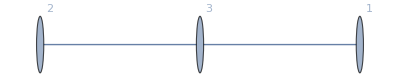
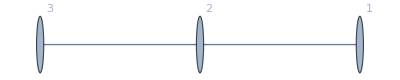
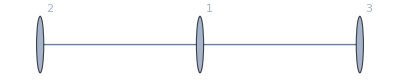
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(GraphFromStabilizer/@stabilisers)⟦;;,1⟧
```

#### State from circuit

```mathematica
stabilisers=FindStabilizer[expψ]
```

{{{𝕀,𝕀,𝕀,𝕀,𝕀,𝕀},{𝕀,𝕀,𝕀,𝕀,X,Z},{𝕀,𝕀,𝕀,X,𝕀,Z},{𝕀,𝕀,𝕀,X,X,𝕀},{𝕀,𝕀,X,𝕀,𝕀,Z},{𝕀,𝕀,X,𝕀,X,𝕀},{𝕀,𝕀,X,X,𝕀,𝕀},{𝕀,𝕀,X,X,X,Z},{𝕀,X,𝕀,𝕀,𝕀,Z},{𝕀,X,𝕀,𝕀,X,𝕀},{𝕀,X,𝕀,X,𝕀,𝕀},{𝕀,X,𝕀,X,X,Z},{𝕀,X,X,𝕀,𝕀,𝕀},{𝕀,X,X,𝕀,X,Z},{𝕀,X,X,X,𝕀,Z},{𝕀,X,X,X,X,𝕀},{Z,Z,Z,Z,Z,X},{X,𝕀,𝕀,𝕀,𝕀,Z},{X,𝕀,𝕀,𝕀,X,𝕀},{X,𝕀,𝕀,X,𝕀,𝕀},{X,𝕀,𝕀,X,X,Z},{X,𝕀,X,𝕀,𝕀,𝕀},{X,𝕀,X,𝕀,X,Z},{X,𝕀,X,X,𝕀,Z},{X,𝕀,X,X,X,𝕀},{X,X,𝕀,𝕀,𝕀,𝕀},{X,X,𝕀,𝕀,X,Z},{X,X,𝕀,X,𝕀,Z},{X,X,𝕀,X,X,𝕀},{X,X,X,𝕀,𝕀,Z},{X,X,X,𝕀,X,𝕀},{X,X,X,X,𝕀,𝕀},{X,X,X,X,X,Z}},718,{{𝕀,𝕀,𝕀,𝕀,𝕀,𝕀},{𝕀,𝕀,𝕀,𝕀,X,X},{𝕀,𝕀,𝕀,X,𝕀,X},27,{Z,X,X,𝕀,X,𝕀},{Z,X,X,X,𝕀,𝕀},{Z,X,X,X,X,X}}}
 |  |  |  |

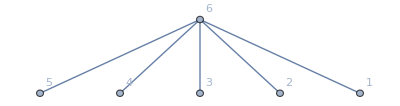
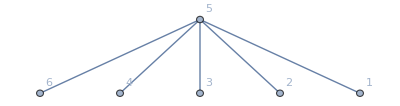
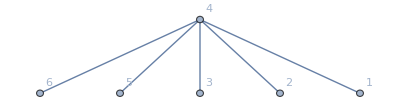
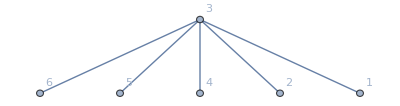
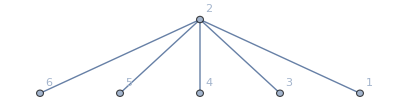
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(GraphFromStabilizer/@stabilisers)⟦;;,1⟧
```

## One Bell pair

### Creating alternate circuit

#### Creating the circuit

```mathematica
input=(1/√2(w[0,1,H]+w[0,1,V])1/√2(w[0,2,H]+w[0,2,V])1/√2(w[0,3,H]w[0,4,H]+w[0,3,V]w[0,4,V])1/√2(w[0,5,H]+w[0,5,V])1/√2(w[0,6,H]+w[0,6,V]));
```

```mathematica
output=((#
/.PBS[0,2,3,0]
/.PBS[0,4,5,0]
/.PBS[0,3,4,0]//Expand)/.DumpHO//Simplify//Chop)&@input//Expand
```

(w[0,1,H] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,H])/(4 √2)+(w[0,1,V] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,H])/(4 √2)-(w[0,1,H] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,H])/(4 √2)-(w[0,1,V] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,H])/(4 √2)+(w[0,1,H] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,V])/(4 √2)+(w[0,1,V] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,V])/(4 √2)-(w[0,1,H] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,V])/(4 √2)-(w[0,1,V] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,V])/(4 √2)

```mathematica
outputState=PostSelection[output,w[0,1,_]w[0,2,_]w[0,3,_]w[0,4,_]w[0,5,_]w[0,6,_]]
```

(w[0,1,H] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,H])/(4 √2)+(w[0,1,V] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,H])/(4 √2)-(w[0,1,H] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,H])/(4 √2)-(w[0,1,V] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,H])/(4 √2)+(w[0,1,H] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,V])/(4 √2)+(w[0,1,V] w[0,2,H] w[0,3,H] w[0,4,H] w[0,5,H] w[0,6,V])/(4 √2)-(w[0,1,H] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,V])/(4 √2)-(w[0,1,V] w[0,2,V] w[0,3,V] w[0,4,V] w[0,5,V] w[0,6,V])/(4 √2)

#### Ket state from optical circuit

```mathematica
Sqrt@SuccessProbability[outputState]
```

1/2

```mathematica
expψ=(Sqrt@ModeOperatorationToState[outputState]⟦1⟧)*ModeOperatorationToState[outputState]⟦2⟧
```

{{1/2},{1/2},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-1/2},{-1/2},{1/2},{1/2},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{-1/2},{-1/2}}

```mathematica
expψ*Coding[6]//Total
```

{(|000000⟩)/2+(|000001⟩)/2-(|011110⟩)/2-(|011111⟩)/2+(|100000⟩)/2+(|100001⟩)/2-(|111110⟩)/2-(|111111⟩)/2}

```mathematica
expρ=DensityMatrix[expψ];
```

```mathematica
Purity[expρ]
```

4

#### Density Matrix Plot

```mathematica
MatrixPlot[expρ,ColorFunction->"ValentineTones",PlotLegends->Automatic,PlotRangePadding->Scaled[.0],FrameLabel->{"Index","Index"},FrameTicks->{All,All}]
```

-Graphics-

### Finding equivalent graph

#### Functions

```mathematica
kron[u__]:=KroneckerProduct[u];
dlist[n_]:=kron@@Table[d,{n}];
```

```mathematica
Block[{list,iMatrix,jMatrix,i,j,n},
Mproduct[iMatrix_,jMatrix_,i_,j_,n_]:=(
list=Table[s0,{n}];
list⟦i⟧=iMatrix;
list⟦j⟧=jMatrix;
Return[list];
);
];

CZ=1/2(kron@@Mproduct[s0,s0,#1,#2,#3]+kron@@Mproduct[sz,s0,#1,#2,#3]+kron@@Mproduct[s0,sz,#1,#2,#3]-kron@@Mproduct[sz,sz,#1,#2,#3])&; 
(*CZ=|0x0| x I+|1x1| x Z = II+ZI+IZ+ZZ*)

Module[{graph,l,ListTheEdge,CZlist,G},
ClusterGenerator[graph_,n_]:=(
l=EdgeList[graph];
ListTheEdge=Table[{l⟦i,1⟧,l⟦i,2⟧},{i,1,Length[l]}];

CZlist=Table[
	CZ@@{ListTheEdge⟦i,1⟧,ListTheEdge⟦i,2⟧,n},{i,1,Length@ListTheEdge}];

G=Dot@@CZlist;
Return[G];
);
];
```

```mathematica
FindStabilizer[state_]:=Module[{dim,ops,stabpos,stabpos2,stablistRaw,stablist,stablist2,stablist3,pos,stablistCut1,pos2},
(* determine the state-dimensions *)
dim=1/Log[Length[state],2];
(* set up the list of combinations of Pauli operators for each qubit *)
ops=Nest[Kronk[{#,{s0,sx,sy,sz}}]&,{s0,sx,sy,sz},dim-1];
(* solve the system of eigenvalue problems & find zeros *)
stabpos=Flatten[Position[(NMinimize[Norm[#.state-(Exp[I ϕ]state)],ϕ][[1]]//Chop)&/@ops,0]];
(* Extract the operators that solve the eigenvalue problem -- map the index of the equation to d pauli operators *)
stabpos2=(Reverse[Table[Mod[Floor[(#-1)/4^ind],4]+1,{ind,0,dim-1}]]&/@Flatten[stabpos]);
(* Map the indices to symbols *)
stablistRaw=stabpos2/.{1->𝕀,2->X,3->Y,4->Z};
(* Now the fun starts *)
(* Apply one hada sequentially to every set of operators *)
stablist2=Table[Join[#[[;;i-1]],{#[[i]]/.{𝕀->𝕀,X->Z,Y->Y,Z->X}},#[[i+1;;]]]&/@#,{i,1,dim}]&@stablistRaw;
(* Apply one hada sequentially to every set of operators from before, until H x H x H ... x H has been applide *)
(* This step can be mad more efficient --- a lot of overhead here *)
stablist3=Flatten[NestList[Flatten[Table[Join[#[[;;i-1]],{#[[i]]/.{𝕀->𝕀,X->Z,Y->Y,Z->X}},#[[i+1;;]]]&/@#&/@#,{i,1,dim}],1]&,stablist2,dim-1],1];
(* Delete all operators that contain a Y -- these are not useful for finding the graph *)
stablist=DeleteCases[#,{___,Y,___}]&/@Join[{stablistRaw},stablist3];
(* Find the position of all sets of operators that have exactly one X-operator per vertex *)
pos=Flatten[Position[Count[#,1]&/@(Count[#,X]&/@#&/@stablist),x_/;x==dim]];
(* Output the candidate sets of operators *)
stablistCut1=stablist[[#]]&/@pos;

(* This throws away all the cases which do not contain an X for each node *)
pos2=Flatten[Position[Total/@((ReplaceAll[#,{𝕀->0,X->1,Y->0,Z->0}]&/@stablistCut1)(ReplaceAll[(Total/@#),x_/;x>1->0]&/@(ReplaceAll[#,{𝕀->0,X->1,Y->0,Z->0}]&/@stablistCut1))),Table[1,{i,1,dim}]]];
stablistCut1[[#]]&/@pos2
];
```

```mathematica
GraphFromStabilizer[stabs_]:=Block[{stablist,posX,posZ,edgelist},
stablist=stabs[[Position[Count[#,X]&/@stabs,1]//Flatten]];
posX=Position[#,X]&/@stablist;
posZ=Position[#,Z]&/@stablist;
edgelist=Flatten[Table[(posX[[ind,1,1]]<->#[[1]])&/@posZ[[ind]],{ind,1,Length[stablist]}]];
DrawGraph[DeleteDuplicates[Sort/@edgelist]]
];
```

```mathematica
Block[{graph,vertex,g,ClusterState,ClusterStateHVbasis},
DrawGraph[edgelist_]:=(

graph=Graph[edgelist,VertexLabels->"Name"];
vertex=VertexCount[graph];

g=ClusterGenerator[graph,vertex];
ClusterState=g.dlist[vertex];

ClusterStateHVbasis=Table[ClusterState⟦i⟧*IntegerString[i-1,2,vertex],{i,1,2^vertex}];

Return[{graph,ClusterState,ClusterStateHVbasis}];

);
];
```

#### State from circuit

```mathematica
stabilisers=FindStabilizer[expψ]
```

{{{𝕀,𝕀,𝕀,𝕀,𝕀,𝕀},{𝕀,𝕀,𝕀,𝕀,𝕀,X},{𝕀,𝕀,𝕀,X,Z,𝕀},{𝕀,𝕀,𝕀,X,Z,X},{𝕀,𝕀,X,𝕀,Z,𝕀},{𝕀,𝕀,X,𝕀,Z,X},{𝕀,𝕀,X,X,𝕀,𝕀},{𝕀,𝕀,X,X,𝕀,X},{𝕀,Z,Z,Z,X,𝕀},{𝕀,Z,Z,Z,X,X},{𝕀,X,𝕀,𝕀,Z,𝕀},{𝕀,X,𝕀,𝕀,Z,X},{𝕀,X,𝕀,X,𝕀,𝕀},{𝕀,X,𝕀,X,𝕀,X},{𝕀,X,X,𝕀,𝕀,𝕀},{𝕀,X,X,𝕀,𝕀,X},{𝕀,X,X,X,Z,𝕀},{𝕀,X,X,X,Z,X},{X,𝕀,𝕀,𝕀,𝕀,𝕀},{X,𝕀,𝕀,𝕀,𝕀,X},{X,𝕀,𝕀,X,Z,𝕀},{X,𝕀,𝕀,X,Z,X},{X,𝕀,X,𝕀,Z,𝕀},{X,𝕀,X,𝕀,Z,X},{X,𝕀,X,X,𝕀,𝕀},{X,𝕀,X,X,𝕀,X},{X,Z,Z,Z,X,𝕀},{X,Z,Z,Z,X,X},{X,X,𝕀,𝕀,Z,𝕀},{X,X,𝕀,𝕀,Z,X},{X,X,𝕀,X,𝕀,𝕀},{X,X,𝕀,X,𝕀,X},{X,X,X,𝕀,𝕀,𝕀},{X,X,X,𝕀,𝕀,X},{X,X,X,X,Z,𝕀},{X,X,X,X,Z,X}},982,{{𝕀,𝕀,𝕀,𝕀,𝕀,𝕀},{𝕀,𝕀,𝕀,𝕀,𝕀,X},33,{X,Z,X,X,X,X}}}
 |  |  |  |

```mathematica
(GraphFromStabilizer/@stabilisers)⟦;;,1⟧
```

Set::partw: Part 5 of {{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}}} does not exist.

Set::partw: Part 5 of {{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,-1}}} does not exist.

Set::partw: Part 5 of {{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}},{{1,0},{0,1}}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}